### Origin Data

### only two column

```mathematica
SystemDialogInput["FileOpen"]
Import[%,"Data"]
ListOrigin=%
```

C:\Users\86153\Desktop\程序包开发\Thermal_0.1\data file\ka-_0_5.txt

{{0.25,0.3,15.2181,0.02451,0.9979},{0.3,0.35,14.6217,0.02032,0.9052},{0.35,0.4,13.5181,0.01713,0.81197},{0.4,0.45,11.9029,0.01443,0.7042},{0.45,0.5,10.3337,0.01227,0.60693},{0.5,0.55,9.2256,0.01072,0.53991},{0.55,0.6,7.9082,0.00927,0.46283},{0.6,0.65,6.5213,0.00792,0.38064},{0.65,0.7,5.423,0.00684,0.31653},{0.7,0.75,4.5785,0.00598,0.26724},{0.4,0.5,10.8061,0.0122,0.6365},{0.5,0.6,8.2461,0.00902,0.48198},{0.6,0.7,5.9866,0.00675,0.3493},{0.7,0.8,4.1978,0.00509,0.24488},{0.8,0.9,2.9062,0.00389,0.16962},{0.9,1.,2.0117,0.00302,0.11762},{1.,1.1,1.3985,0.00237,0.0822},{1.1,1.2,0.9717,0.00187,0.05798},{1.2,1.3,0.66,0.00146,0.04108},{1.3,1.4,0.4546,0.00116,0.03148},{1.4,1.5,0.3111,0.00092,0.02696},{1.5,1.6,0.2162,0.00074,0.01873},{1.6,1.7,0.1484,0.00059,0.01286},{1.7,1.8,0.1011,0.00048,0.00877},{1.8,1.9,0.0688,0.00038,0.00597},{1.9,2.,0.0476,0.00031,0.00413}}

{{0.25,0.3,15.2181,0.02451,0.9979},{0.3,0.35,14.6217,0.02032,0.9052},{0.35,0.4,13.5181,0.01713,0.81197},{0.4,0.45,11.9029,0.01443,0.7042},{0.45,0.5,10.3337,0.01227,0.60693},{0.5,0.55,9.2256,0.01072,0.53991},{0.55,0.6,7.9082,0.00927,0.46283},{0.6,0.65,6.5213,0.00792,0.38064},{0.65,0.7,5.423,0.00684,0.31653},{0.7,0.75,4.5785,0.00598,0.26724},{0.4,0.5,10.8061,0.0122,0.6365},{0.5,0.6,8.2461,0.00902,0.48198},{0.6,0.7,5.9866,0.00675,0.3493},{0.7,0.8,4.1978,0.00509,0.24488},{0.8,0.9,2.9062,0.00389,0.16962},{0.9,1.,2.0117,0.00302,0.11762},{1.,1.1,1.3985,0.00237,0.0822},{1.1,1.2,0.9717,0.00187,0.05798},{1.2,1.3,0.66,0.00146,0.04108},{1.3,1.4,0.4546,0.00116,0.03148},{1.4,1.5,0.3111,0.00092,0.02696},{1.5,1.6,0.2162,0.00074,0.01873},{1.6,1.7,0.1484,0.00059,0.01286},{1.7,1.8,0.1011,0.00048,0.00877},{1.8,1.9,0.0688,0.00038,0.00597},{1.9,2.,0.0476,0.00031,0.00413}}

### five column (pt-,pt+,exper,err,err)

```mathematica
SystemDialogInput["FileOpen"]
Import[%,"Data"]
ListOrigin={(#[[1]]+#[[2]])/2,#[[3]]}&/@%
```

C:\Users\86153\Desktop\程序包开发\Thermal_0.1\data file\ka+_0_5.txt

{{0.25,0.3,19.1716,0.02751,1.25715},{0.3,0.35,18.3834,0.02279,1.13808},{0.35,0.4,16.9151,0.01916,1.01602},{0.4,0.45,15.0058,0.0162,0.88776},{0.45,0.5,13.1072,0.01382,0.76977},{0.5,0.55,11.6066,0.01202,0.67928},{0.55,0.6,9.9435,0.01039,0.5809},{0.6,0.65,8.4206,0.009,0.49147},{0.65,0.7,6.8518,0.00768,0.39981},{0.7,0.75,6.0383,0.00686,0.35266},{0.4,0.5,13.6238,0.0135,0.80247},{0.5,0.6,10.5041,0.01007,0.61395},{0.6,0.7,7.695,0.00759,0.44898},{0.7,0.8,5.4354,0.00574,0.31707},{0.8,0.9,3.7889,0.0044,0.22114},{0.9,1.,2.6372,0.00341,0.15419},{1.,1.1,1.8393,0.00267,0.10811},{1.1,1.2,1.2702,0.00209,0.07579},{1.2,1.3,0.8615,0.00163,0.05362},{1.3,1.4,0.5883,0.00128,0.04073},{1.4,1.5,0.4014,0.00101,0.03478},{1.5,1.6,0.2748,0.0008,0.02381},{1.6,1.7,0.1871,0.00064,0.01622},{1.7,1.8,0.127,0.0005,0.01101},{1.8,1.9,0.0852,0.0004,0.00739},{1.9,2.,0.0581,0.00032,0.00504}}

{{0.55,19.1716},{0.65,18.3834},{0.75,16.9151},{0.85,15.0058},{0.95,13.1072},{1.05,11.6066},{1.15,9.9435},{1.25,8.4206},{1.35,6.8518},{1.45,6.0383},{0.9,13.6238},{1.1,10.5041},{1.3,7.695},{1.5,5.4354},{1.7,3.7889},{1.9,2.6372},{2.1,1.8393},{2.3,1.2702},{2.5,0.8615},{2.7,0.5883},{2.9,0.4014},{3.1,0.2748},{3.3,0.1871},{3.5,0.127},{3.7,0.0852},{3.9,0.0581}}

### Meson

```mathematica
Once[SystemDialogInput["FileOpen"]]
Import@%
StringSplit[StringSplit[%,"\n"]];
ListLabel=%[[1]];
ListData=ToExpression@StringReplace[#,"E"->"*^"]&/@%%[[2;;]];
```

D:\大创\prog_chisq\dNptdpt_AuAu39 _pion_c025.txt

%pt            TT            TS            SS            SS2j            Tot
       0.2750    1.88588E+02    1.51506E-15    1.01818E-16    9.80147E-34    1.88588E+02
       0.3250    1.46114E+02    1.12116E-15    8.61538E-17    6.85152E-34    1.46114E+02
       0.3750    1.13348E+02    8.90166E-16    7.46667E-17    5.35211E-34    1.13348E+02
       0.4250    8.80422E+01    6.93192E-16    6.58824E-17    4.08516E-34    8.80422E+01
       0.4750    6.84763E+01    5.65077E-16    5.89474E-17    3.36506E-34    6.84763E+01
       0.5250    5.33305E+01    4.54827E-16    5.33333E-17    2.70899E-34    5.33305E+01
       0.5750    4.15920E+01    3.78072E-16    4.86957E-17    2.30941E-34    4.15920E+01
       0.6250    3.24828E+01    3.11649E-16    4.48000E-17    1.92676E-34    3.24828E+01
       0.6750    2.54049E+01    2.63115E-16    4.14815E-17    1.68248E-34    2.54049E+01
       0.7250    1.98980E+01    2.20926E-16    3.86207E-17    1.44012E-34    1.98980E+01
       0.4500    7.76325E+01    6.16503E-16    6.22222E-17    3.61350E-34    7.76325E+01
       0.5500    4.70888E+01    4.10256E-16    5.09091E-17    2.45037E-34    4.70888E+01
       0.6500    2.87215E+01    2.84091E-16    4.30769E-17    1.76998E-34    2.87215E+01
       0.7500    1.76194E+01    2.03083E-16    3.73333E-17    1.33803E-34    1.76194E+01
       0.8500    1.08723E+01    1.49077E-16    3.29412E-17    1.04682E-34    1.08723E+01
       0.9500    6.74864E+00    1.11955E-16    2.94737E-17    8.41265E-35    6.74864E+00
       1.0500    4.21376E+00    8.57717E-17    2.66667E-17    6.90794E-35    4.21376E+00
       1.1500    2.64633E+00    6.68875E-17    2.43478E-17    5.77352E-35    2.64633E+00
       1.2500    1.67136E+00    5.29960E-17    2.24000E-17    4.89718E-35    1.67136E+00
       1.3500    1.06135E+00    4.25949E-17    2.07407E-17    4.20619E-35    1.06135E+00
       1.4500    6.77486E-01    3.46814E-17    1.93103E-17    3.65174E-35    6.77486E-01
       1.5500    4.34571E-01    2.85720E-17    1.80645E-17    3.20011E-35    4.34571E-01
       1.6500    2.80028E-01    2.37917E-17    1.69697E-17    2.82735E-35    2.80028E-01
       1.7500    1.81206E-01    2.00050E-17    1.60000E-17    2.51611E-35    1.81206E-01
       1.8500    1.17713E-01    1.69710E-17    1.51351E-17    2.25358E-35    1.17713E-01
       1.9500    7.67373E-02    1.45145E-17    1.43590E-17    2.03008E-35    7.67373E-02

#### Plot

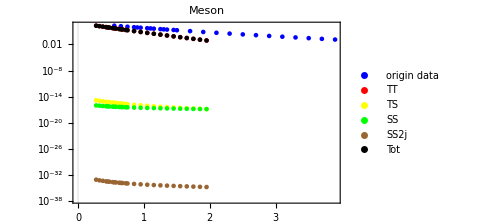

mesonplot.eps

```mathematica
Show[{
ListLogPlot[{ListOrigin}~Join~Table[ListData[[All,{1,col}]],{col,2,6}],PlotLabel->"Meson",PlotLegends->PointLegend[ReplacePart[ListLabel,1->"origin data"],LegendFunction->(Framed[#,Background->White]&)],PlotStyle->{Blue,Red,Yellow,Green,Brown,Black},PlotTheme->"Scientific",Background->White]
},ImageSize->Medium,Background->White,Frame->True]
Export["mesonplot.eps",%]
```

### Baryon

```mathematica
SystemDialogInput["FileOpen"]
Import@%
StringSplit[StringSplit[%,"\n"]];
ListLabel=%[[1]];
ListData=ToExpression@StringReplace[#,"E"->"*^"]&/@%%[[2;;]];
```

D:\大创\prog_chisq\dNptdpt_AuAu39 _xibar_c025.txt

%pt           TTT           TTS           TSS           TSS2j           SSS           SSS2j           Tot
       0.8016    1.13968E-01    3.65650E-18    3.11610E-18    0.00000E+00    6.80506E-19    0.00000E+00    1.13968E-01
       1.1470    6.41372E-02    2.10612E-18    1.78375E-18    0.00000E+00    4.19732E-19    0.00000E+00    6.41372E-02
       1.4443    3.32838E-02    1.20776E-18    1.09990E-18    0.00000E+00    2.97777E-19    0.00000E+00    3.32838E-02
       1.7422    1.58454E-02    6.64949E-19    6.80148E-19    0.00000E+00    2.20901E-19    0.00000E+00    1.58454E-02
       2.0406    7.13435E-03    3.57484E-19    4.23171E-19    0.00000E+00    1.69575E-19    0.00000E+00    7.13435E-03
       2.3801    2.75286E-03    1.73645E-19    2.49105E-19    0.00000E+00    1.27940E-19    0.00000E+00    2.75286E-03
       2.8544    6.90321E-04    6.23798E-20    1.21010E-19    0.00000E+00    9.06314E-20    0.00000E+00    6.90321E-04
       3.5191    9.29814E-05    1.46854E-20    4.50124E-20    0.00000E+00    6.01353E-20    0.00000E+00    9.29814E-05
       4.3767    6.52828E-06    0.00000E+00    1.31154E-20    0.00000E+00    3.83977E-20    0.00000E+00    6.52828E-06

#### Plot

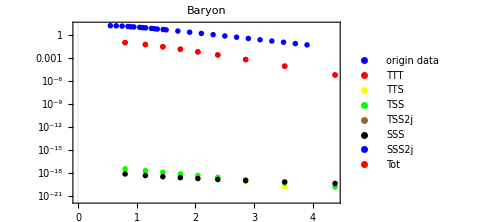

baryonplot.eps

```mathematica
Show[{
ListLogPlot[{ListOrigin}~Join~Table[ListData[[All,{1,col}]],{col,2,8}],PlotLabel->"Baryon",PlotLegends->PointLegend[ReplacePart[ListLabel,1->"origin data"],LegendFunction->(Framed[#,Background->White]&)],PlotStyle->{Blue,Red,Yellow,Green,Brown,Black},PlotTheme->"Scientific",Background->White]
},ImageSize->Medium,Background->White,Frame->True]
Export["baryonplot.eps",%]
```